```mathematica
Needs["nanowire`",NotebookDirectory[]<>"nanowire.wl"]
```

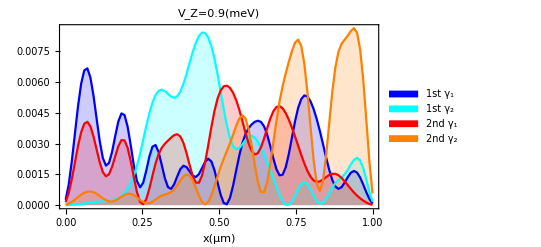

```mathematica
wfm=wfmajoranaqd[1,1,.9,25,1.1,100,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp17\\bad-inhom\\2\\m1.0D0.2a5L100expmx-1.0sg20.0V0.9.png",wfm]
```

D:\CMTC\bothlead\Rp17\bad-inhom\2\m1.0D0.2a5L100expmx-1.0sg20.0V0.9.png

```mathematica
?wfmajoranamu
```

wfmajoranamu[a,μ,vz,mumax,sigma,dim,index]; WF for inhomogeneous potential, index for first one or two state(s)

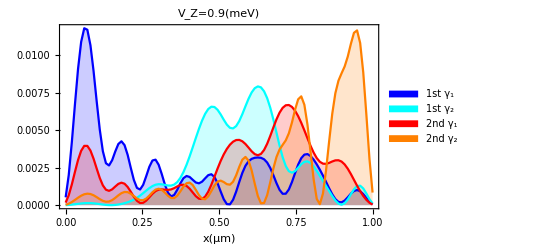

```mathematica
wfm=wfmajoranamu[1,1,.9,-1.,20,100,2]
```

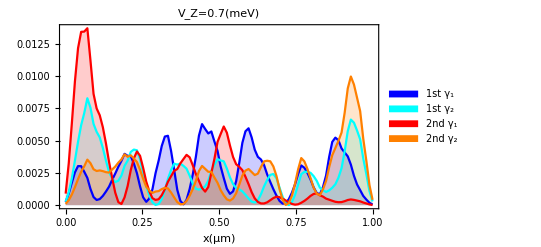

```mathematica
wfm=wfmajoranadis[1,1,.7,vimplist,100,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp17\\ugly\\2\\m1.0D0.2a5L100v1.0V0.7.png",wfm]
```

D:\CMTC\bothlead\Rp17\ugly\2\m1.0D0.2a5L100v1.0V0.7.png

0.00409008

0.0370881

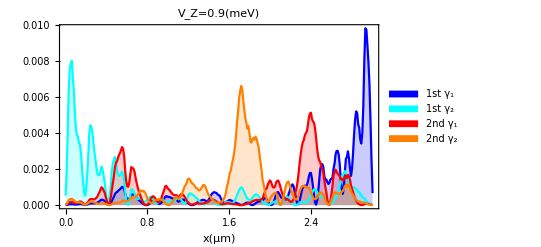

```mathematica
wfm=wfmajoranasedis[1,1,0.9,vimplist,.2,{0.004118498324578,0.010087805951677},3,300,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\ugly\\1\\m1.0D0.2a5L300v1.0g0.2Vc3V0.7.png",wfm]
```

D:\CMTC\bothlead\Rp16\ugly\1\m1.0D0.2a5L300v1.0g0.2Vc3V0.7.png

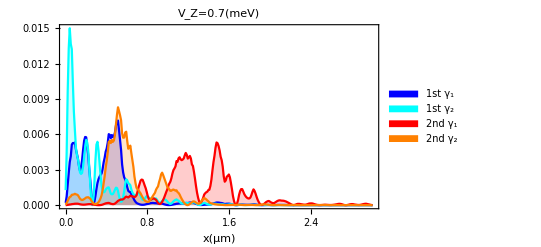

```mathematica
wfm=wfmajoranasedis[1,1,0.7,vimplist,.2,{0.012472283690042,0.022679178594877},3,300,2]
```

```mathematica
es=Eigensystem[Hseqd[1,1,.7,1.7,20,.2,.0060,3,100],-6,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];
```

```mathematica
es[[2,Nearest[es[[1]]->Automatic,0.006,1][[1]]]]
```

{-0.00650216,-0.0111414,-0.0139899,-0.0150878,-0.0144483,-0.0120682,-0.00794364,-0.00208965,0.00543625,0.0145101,0.024919,0.0363433,0.0483485,0.0603882,0.071824,0.0819619,0.0901061,0.0956261,0.0980327,0.0970529,0.0925386,0.0829143,0.0698551,0.0553166,0.0413073,0.0296615,0.0218385,0.018767,0.0207549,0.0274696,0.0379915,0.0509323,0.0646034,0.0772151,0.0870819,0.0928139,0.0934698,0.0886576,0.0785717,0.0639639,0.0460522,0.0263802,0.0066421,-0.0115052,-0.0266225,-0.0376405,-0.0439679,-0.045544,-0.0428303,-0.0367444,-0.0285437,-0.019673,-0.0115943,-0.00561755,-0.00275161,-0.00359238,-0.00825925,-0.0163869,-0.0271725,-0.0394716,-0.0519327,-0.0631526,-0.0718367,-0.0769455,-0.0778103,-0.0742063,-0.0663748,-0.0549927,-0.0410938,-0.02595,-0.010928,0.00266404,0.0137204,0.0214582,0.0254994,0.0259056,0.0231633,0.0181205,0.0118816,0.00567582,0.000709873,-0.00197412,-0.00162213,0.00214213,0.00927112,0.0192962,0.0313786,0.0444029,0.0571022,0.0682007,0.076558,0.0812976,0.0819064,0.0782926,0.0707964,0.0601513,0.0474017,0.0337837,0.020586,0.00900308,-0.0105804,-0.0222755,-0.0347166,-0.0475306,-0.0603209,-0.0726515,-0.0840359,-0.093935,-0.101765,-0.106916,-0.108792,-0.106854,-0.100682,-0.0900403,-0.0749461,-0.0557242,-0.0330467,-0.00794216,0.0182326,0.0438628,0.0669591,0.0839727,0.0930197,0.0931429,0.0843979,0.067824,0.0453059,0.0193442,-0.00723801,-0.0316168,-0.0512829,-0.0643143,-0.0695766,-0.066831,-0.0567396,-0.0407694,-0.0210082,0.0000848886,0.0199654,0.0362929,0.0471909,0.0514496,0.0486491,0.0391909,0.0242363,0.00556064,-0.0146597,-0.0341012,-0.0505588,-0.0621942,-0.0677375,-0.0666215,-0.0590347,-0.0458873,-0.0286965,-0.0094058,0.00984239,0.0269519,0.0401092,0.0479844,0.0498741,0.0457712,0.0363543,0.0229,0.00712764,-0.00900379,-0.0235237,-0.0346766,-0.0411213,-0.0420809,-0.0374267,-0.0276872,-0.0139817,0.00211278,0.018746,0.0340087,0.046152,0.0537873,0.0560431,0.052662,0.0440272,0.0311152,0.0153809,-0.00141137,-0.0173916,-0.0307992,-0.0401849,-0.044576,-0.0435867,-0.037461,-0.0270423,-0.0136749,0.000952235,0.0150024,0.026704,0.0345573,0.0375096,0.0350801,0.0274186,0.0152921,0.0112895,0.0241684,0.0382588,0.0531837,0.0685446,0.0839017,0.0987587,0.112554,0.124665,0.134423,0.141145,0.144181,0.142972,0.137125,0.126483,0.111193,0.0917624,0.0690796,0.0444033,0.0193056,-0.00369283,-0.0228125,-0.0361976,-0.0426934,-0.041945,-0.0344051,-0.0212551,-0.00424921,0.0144966,0.032747,0.048394,0.0596793,0.0653714,0.0648793,0.0582917,0.0463435,0.0303127,0.0118642,-0.00714149,-0.0248536,-0.0396258,-0.0501821,-0.0557362,-0.0560532,-0.0514518,-0.042746,-0.0311388,-0.0180783,-0.00509504,0.00636209,0.0150739,0.0201683,0.0211957,0.0181572,0.0114844,0.0019759,-0.00930183,-0.0211354,-0.0322952,-0.0416612,-0.0483317,-0.0517035,-0.0515193,-0.047877,-0.0412034,-0.0321967,-0.0217454,-0.0108328,-0.000437166,0.00856173,0.0154618,0.0197963,0.0213664,0.0202465,0.0167641,0.0114571,0.00501454,-0.00179343,-0.008189,-0.0134575,-0.0170088,-0.0184258,-0.0174954,-0.0142212,-0.00881792,-0.0016883,0.00661457,0.0154362,0.0240766,0.0318496,0.0381393,0.042452,0.0444576,0.0440181,0.0412014,0.0362782,0.029702,0.0220741,0.0140935,0.00649831,-0.00890758,-0.0158967,-0.0210756,-0.0245179,-0.0262663,-0.0263423,-0.0247623,-0.0215575,-0.0167991,-0.0106249,-0.00326461,0.00493787,0.0135117,0.021858,0.0292661,0.0349474,0.0380895,0.0379269,0.0338235,0.0253582,0.0128342,-0.0035171,-0.0224053,-0.0422726,-0.0614702,-0.0784377,-0.0918674,-0.100834,-0.104881,-0.104048,-0.0988497,-0.0902019,-0.0793062,-0.0675111,-0.056162,-0.0464575,-0.0393289,-0.0353521,-0.0347026,-0.0371555,-0.0421278,-0.0487578,-0.0560115,-0.0628018,-0.0681085,-0.0710865,-0.0711496,-0.0680233,-0.0617625,-0.0527332,-0.0415623,-0.0290623,-0.0161403,-0.00370137,0.00744283,0.0166513,0.0235093,0.0278574,0.029793,0.0296453,0.027928,0.0252759,0.022373,0.0198795,0.0183663,0.0182613,0.0198144,0.0230817,0.0279297,0.0340583,0.0410379,0.048357,0.055474,0.0618692,0.0670906,0.0707911,0.0727532,0.0729006,0.0712976,0.068135,0.0637075,0.0583834,0.0525705,0.0466805,0.0410959,0.0361401,0.0320545,0.0289812,0.0269552,0.0259034,0.0256523,0.025942,0.0264479,0.0268058,0.0266417,0.0256027,0.0233881,0.0197773,0.0146528,0.00801721}

```mathematica
?wfmajoranasemu
```

wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_,index_]; WF for wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_,index_]

ω0=0.003ω1=0.00336896

ω0=0.036ω1=0.0346808

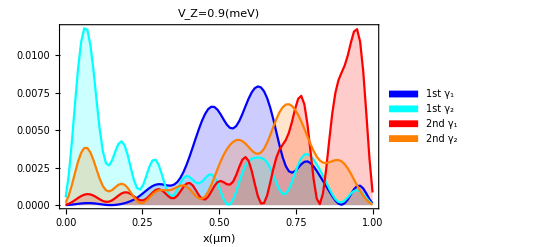

```mathematica
wfm=wfmajoranasemu[1,1,.9,-1.,20,0.2,{.0030,.0360},∞,100,2]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp17\\bad-inhom\\2\\m1.0D0.2a5L100expmx-1sg20.0g0.2Vc1.0V0.9.png",wfm]
```

D:\CMTC\bothlead\Rp17\bad-inhom\2\m1.0D0.2a5L100expmx-1sg20.0g0.2Vc1.0V0.9.png

```mathematica
Clear[es]
```

```mathematica
es[[1]]
```

{-0.826271,0.817749,-0.668406,0.659884,-0.658434,0.649912,-0.541739,0.533217,-0.477603,0.46908,-0.315694,0.307172,-0.283284,0.274761,-0.21249,0.203967,-0.172342,0.16382,-0.126952,0.11843}

```mathematica
ii
```

9

```mathematica
wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_?IntegerQ,index_?IntegerQ]:=Block[{testp,testn,g,gamma,test,gamma1,gamma2,(*,es*)},g=Table[es=Eigensystem[Hsemu[a,μ,vz,mumax,sigma,γ,ω⟦i⟧,Vc,dim],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];ii=Nearest[es[[1]]->Automatic,ω[[i]],1][[1]];testp=es[[All,ii]];If[Abs[ω[[i]]-testp[[1]]]>10^-4,Print["ω0=",ω[[i]],"ω1=",testp[[1]]]];gamma=KroneckerProduct[1/2 ConjugateTranspose[{{1,ⅈ,0,0},{0,0,1,ⅈ},{0,0,1,-ⅈ},{-1,ⅈ,0,0}}],IdentityMatrix[dim,SparseArray]].testp⟦2⟧;{Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{1,3}⟧],Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{2,4}⟧]},{i,index}];gamma1=g⟦All,1⟧;gamma2=g⟦All,2⟧;ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma1,gamma2}]],1],DataRange->{0,(dim a)/100},PlotLabel->"\!\(\*SubscriptBox[\(V\), \(Z\)]\)="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,Filling->Axis,PlotLegends->Placed[SwatchLegend[{"1st \!\(\*SubscriptBox[\(γ\), \(1\)]\)","1st \!\(\*SubscriptBox[\(γ\), \(2\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(1\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(2\)]\)"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->{Blue,Cyan,Red,Orange}]]
```

```mathematica
Hsemu[a_?NumberQ,μ0_?NumberQ,V0_?NumberQ,mumax_,sigma_,γ_,ω_,Vc_,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=5/(2 a),Vz=V0,Δ=.2,mux},mux=mumax Exp[-#1^2/(2 sigma^2)]+μ&;Δ=If[V0<Vc,Δ √(1-(V0/Vc)^2),0];KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}]+(2 t) IdentityMatrix[dim,SparseArray]-DiagonalMatrix[SparseArray[mux[Range[dim]-1]]]]+KroneckerProduct[PauliMatrix[2],ⅈ α SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}]]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz IdentityMatrix[dim,SparseArray]]]-γ Re[(ω IdentityMatrix[4 dim,SparseArray])/(√(Δ^2-ω^2-ⅈ/10^9))+KroneckerProduct[PauliMatrix[1],KroneckerProduct[IdentityMatrix[2],(Δ IdentityMatrix[dim,SparseArray])/(√(Δ^2-ω^2-ⅈ/10^9))]]]]
```

```mathematica
wfmajoranasedis[a_,μ_,vz_,vimp_,γ_,ω_,Vc_,dim_?IntegerQ,index_]:=Block[{testp,testn,g,gamma,test,gamma1,gamma2,es,ii},If[Length[vimp]≠dim,Message[wfmajoranasedis::nnarg,Length[vimp],dim];Throw[$Failed]];g=Table[es=Eigensystem[Hsedis[a,μ,vz,vimp,γ,ω⟦i⟧,Vc,dim],-6,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];ii=Nearest[es[[1]]->Automatic,ω[[i]],1][[1]];testp=es[[All,ii]];If[Abs[ω⟦i⟧-testp⟦1⟧]>1/10^4,Print["ω0=",ω⟦i⟧,"ω1=",testp⟦1⟧]];gamma=KroneckerProduct[1/2 ConjugateTranspose[{{1,ⅈ,0,0},{0,0,1,ⅈ},{0,0,1,-ⅈ},{-1,ⅈ,0,0}}],IdentityMatrix[dim,SparseArray]].testp⟦2⟧;{Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{1,3}⟧],Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{2,4}⟧]},{i,index}];gamma1=g⟦All,1⟧;gamma2=g⟦All,2⟧;ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma1,gamma2}]],1],DataRange->{0,(dim a)/100},PlotLabel->"\!\(\*SubscriptBox[\(V\), \(Z\)]\)="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,Filling->Axis,PlotLegends->Placed[SwatchLegend[{"1st \!\(\*SubscriptBox[\(γ\), \(1\)]\)","1st \!\(\*SubscriptBox[\(γ\), \(2\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(1\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(2\)]\)"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->{Blue,Cyan,Red,Orange}]]
```